## Exoplanetas

```mathematica
Directory[]
```

/Users/michel

```mathematica
NotebookDirectory[]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2023/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2023

```mathematica
Directory[]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2023

```mathematica
exopl=Import["exoplanet.eu_catalog.csv"];
```

```mathematica
header=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_detection_type,radius_detection_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
masas=Select[exopl[[All,3]],NumberQ];
```

```mathematica
Length@masas
```

2990

```mathematica
distmasas=SmoothKernelDistribution[Log10@masas]
```

DataDistribution[…]

```mathematica
10^Mean@distmasas
```

0.570452

```mathematica
Log10@Min[masas]
```

-5.67778

```mathematica
Sort[masas][[1;;10]]
```

{2.1×10^-6,0.000063,0.00007,0.00019,0.00021,0.00082,0.0009,0.00091,0.001041,0.00107}

```mathematica
Reverse[Sort[masas]][[1;;10]]
```

{81.9,70.2,70.,67.,66.95,66.28,66.,64.,63.88,63.4}

```mathematica
Log10@2.1*^-6
```

-5.67778

```mathematica
Log10@Max[masas]
```

1.91328

```mathematica
Log10@Min[masas]
```

-5.67778

Mass Earth / mass Jupiter

WolframAlphaQueryResults

Mass Moon / mass Earth

WolframAlphaQueryResults

0.000063 Mass Jupiter / mass earth

WolframAlphaQueryResults

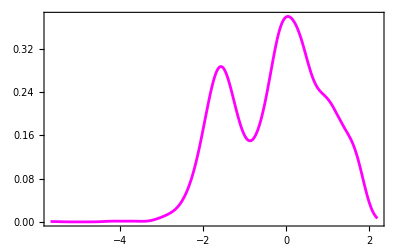

```mathematica
grma=Plot[PDF[distmasas,m],{m,-5.68,2.2},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
FindDistribution[RandomVariate[NormalDistribution[],1000000]]
```

NormalDistribution[0.0111534,1.06169]

```mathematica
FindDistribution[Log10@masas]
```

MixtureDistribution[{0.39089,0.60911},{LogisticDistribution[-1.4156,0.456381],NormalDistribution[0.446576,0.725171]}]

```mathematica
fdist=FindDistribution[Log10@masas,5]
```

{MixtureDistribution[{0.39089,0.60911},{LogisticDistribution[-1.4156,0.456381],NormalDistribution[0.446576,0.725171]}],MixtureDistribution[{0.571003,0.428997},{NormalDistribution[-0.994174,0.965621],NormalDistribution[0.659462,0.666057]}],NormalDistribution[-0.242088,1.13092],StudentTDistribution[-0.28093,1.16763,97.6582],LogisticDistribution[-0.254822,0.692693]}

```mathematica
%//TableForm
```

MixtureDistribution[{0.39089,0.60911},{LogisticDistribution[-1.4156,0.456381],NormalDistribution[0.446576,0.725171]}]
MixtureDistribution[{0.571003,0.428997},{NormalDistribution[-0.994174,0.965621],NormalDistribution[0.659462,0.666057]}]
NormalDistribution[-0.242088,1.13092]
StudentTDistribution[-0.28093,1.16763,97.6582]
LogisticDistribution[-0.254822,0.692693]

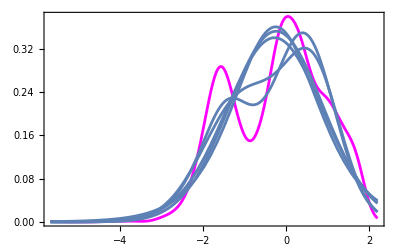

```mathematica
Show[grma,Plot[Table[PDF[fdist[[k]],lgm],{k,5}],{lgm,-5.68,2.2}],PlotRange->All]
```

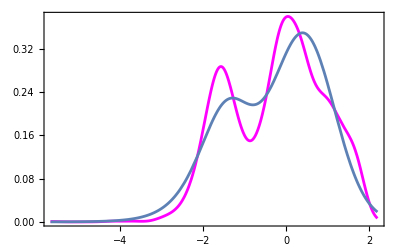

```mathematica
Show[grma,Plot[PDF[fdist[[1]],lgm],{lgm,-5.68,2.2}],PlotRange->All]
```

## Modelo de distribucion de masas de exoplanetas, Bimodal

```mathematica
lg10masas=Log10@masas;
```

```mathematica
lg10masas[[501]]
```

0.024075

```mathematica
PDF[distmasas,lg10masas[[501]]]
```

0.379981

```mathematica
modelo=MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}];
```

```mathematica
PDF[modelo,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2) √(2 π) σ2)

```mathematica
mincuad=Sum[(PDF[distmasas,lg10masas[[k]]]-PDF[modelo,lg10masas[[k]]])^2,{k,Length@lg10masas}];
```

```mathematica
AbsoluteTiming[sol=FindMinimum[mincuad,{{a1,0.5},{a2,0.5},{μ1,-1.5},{σ1,.2},{μ2,-.5},{σ2,.9}}]]
```

{0.50896,{1.91942,{a1→698.016,a2→2544.9,μ1→-1.66212,σ1→0.345815,μ2→0.207166,σ2→0.885438}}}

```mathematica
AbsoluteTiming[sol=NMinimize[mincuad,{{a1,0.,1.},{a2,0.,1.},{μ1,-2.,-1.},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9}},Method->"SimulatedAnnealing"]]
```

{5.75559,{1.91942,{a1→0.381679,a2→1.39156,μ1→-1.66212,σ1→0.345815,μ2→0.207166,σ2→0.885438}}}

```mathematica
sol[[2]]
```

{a1→698.016,a2→2544.9,μ1→-1.66212,σ1→0.345815,μ2→0.207166,σ2→0.885438}

```mathematica
modelo/.sol[[2]]
```

MixtureDistribution[{698.016,2544.9},{NormalDistribution[-1.66212,0.345815],NormalDistribution[0.207166,0.885438]}]

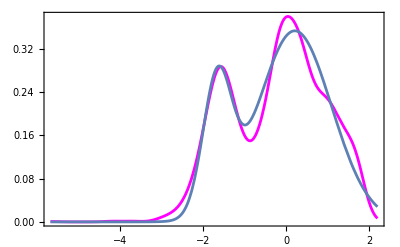

```mathematica
Show[grma,Plot[PDF[modelo/.sol[[2]],lgm],{lgm,-5.68,2.2}]]
```

## Modelo de distribucion de masas de exoplanetas, Trimodal

```mathematica
modelo=MixtureDistribution[{a1,a2,a3},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3]}];
```

```mathematica
PDF[modelo,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3) √(2 π) σ3)

```mathematica
mincuad=Sum[(PDF[distmasas,lg10masas[[k]]]-PDF[modelo,lg10masas[[k]]])^2,{k,Length@lg10masas}];
```

```mathematica
AbsoluteTiming[sol=NMinimize[mincuad,{{a1,0.,1.},{a2,0.,1.},{a3,0.,1.},{μ1,-2.,-1.},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"SimulatedAnnealing"]]
```

{12.8531,{0.0255853,{a1→0.585449,a2→0.858669,a3→0.490827,μ1→-1.57957,σ1→0.427342,μ2→0.00149188,σ2→0.489691,μ3→1.17441,σ3→0.539763}}}

```mathematica
sol[[2]]
```

{a1→0.585449,a2→0.858669,a3→0.490827,μ1→-1.57957,σ1→0.427342,μ2→0.00149188,σ2→0.489691,μ3→1.17441,σ3→0.539763}

```mathematica
modelo/.sol[[2]]
```

MixtureDistribution[{0.585449,0.858669,0.490827},{NormalDistribution[-1.57957,0.427342],NormalDistribution[0.00149188,0.489691],NormalDistribution[1.17441,0.539763]}]

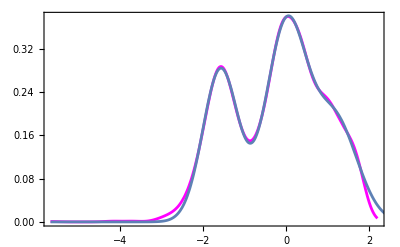

```mathematica
grOLS=Show[grma,Plot[PDF[modelo/.sol[[2]],lgm],{lgm,-5.68,2.5}]]
```

```mathematica
masasT=masas/0.003146;
```

```mathematica
distmasasT=SmoothKernelDistribution[Log10@masasT]
```

DataDistribution[…]

```mathematica
Log10@Min@masasT
```

-3.17554

```mathematica
Log10@Max@masasT
```

4.41553

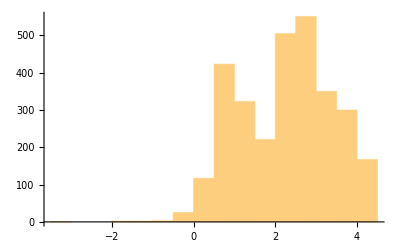

```mathematica
Histogram[Log10@masasT]
```

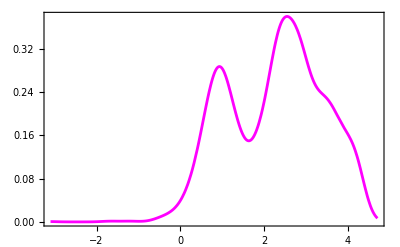

```mathematica
grmaT=Plot[PDF[distmasasT,m],{m,-3.1,4.7},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
PDF[modelo/.sol[[2]],x]
```

0.187485 ⅇ^(-1.71618 (-1.17441+x)^2)+0.361531 ⅇ^(-2.0851 (-0.00149188+x)^2)+0.282459 ⅇ^(-2.73791 (1.57957+x)^2)

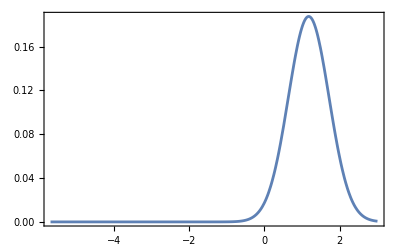
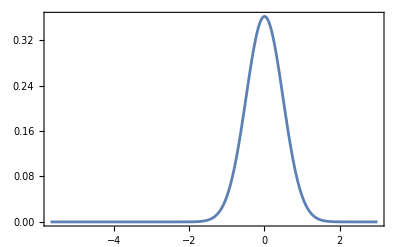
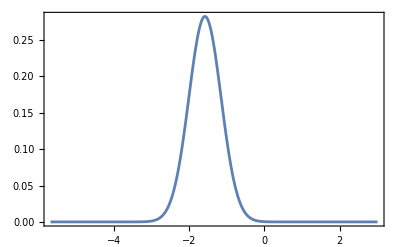

```mathematica
Table[Plot[PDF[modelo/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,Frame->True],{k,3}]
```

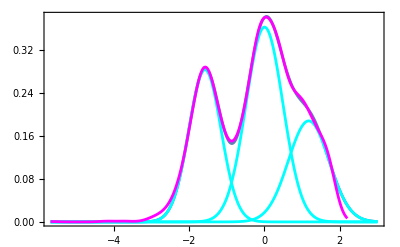

```mathematica
Show[Plot[PDF[modelo/.sol[[2]],lgm],{lgm,-5.68,3},Frame->True],Table[Plot[PDF[modelo/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,PlotStyle->Cyan],{k,3}],grma]
```